# Dynamic simulation of 2 R serial robot

```mathematica
param={l1->0.5,l2->0.3,dia->3*10^-3,g->9.8,ρ->2700}
mass1=((π (dia/2)^2 l1)*ρ)/.param
mass2=((π (dia/2)^2 l2)*ρ)/.param
Inertia1=(mass1(l1^2)/12)/.param
Inertia2=(mass1(l2^2)/12)/.param
massparam={m1->mass1,m2->mass2,I1->Inertia1,I2->Inertia2}
```

{l1→0.5,l2→0.3,dia→3/1000,g→9.8,ρ→2700}

0.00954259

0.00572555

0.000198804

0.0000715694

{m1→0.00954259,m2→0.00572555,I1→0.000198804,I2→0.0000715694}

## Inverse kinematics

```mathematica
IK[{l1_,l2_,x_,y_,θ1_,θ2_}]:=Module[{θ12,ik1,ik2,ik3,ik4,subs,ik5,ik6,t,solth1,solth12,solth2,solns},
ik1 = l1 Cos[θ1]+l2 Cos[θ12]-x;
ik2 = l1 Sin[θ1]+l2 Sin[θ12]-y;
ik3 =Solve[{ik1,ik2}=={0,0},{Cos[θ12],Sin[θ12]}][[1]];
(*Print[ik3]*)
ik4=Simplify[Numerator[Together[(Cos[θ12]^2 +Sin[θ12]^2-1)/.ik3]]];
subs= {Cos[θ1]->(1-t^2)/(1+t^2),Sin[θ1]->2t/(1+t^2)};
ik5=Collect[Numerator[Together[ik4/.subs]],t];
ik6=Solve[ik5==0,t];
solth1={θ1->2*ArcTan[t/.ik6[[1]]],θ1->2*ArcTan[t/.ik6[[2]]]};
solth12={θ12->ArcTan[Cos[θ12],Sin[θ12]]/.ik3/.solth1[[1]],θ12->ArcTan[Cos[θ12],Sin[θ12]]/.ik3/.solth1[[2]]};
solth2={θ2->(θ12-θ1)/.solth1[[1]]/.solth12[[1]],θ2->(θ12-θ1)/.solth1[[2]]/.solth12[[2]]};
solns={{solth1[[1]],solth2[[1]]},{solth1[[2]],solth2[[2]]}};
Return[solns];
]
```

```mathematica
solik=IK[{l1,l2,x,y,θ1,θ2}]/.param/.{x->0.3,y->0.6}
```

{{θ1→0.678034,θ2→1.19537},{θ1→1.53626,θ2→-1.19537}}

```mathematica
cons = {l1 Cos[θ1]+l2 Cos[θ1+θ2]-x,cons2 = l1 Sin[θ1]+l2 Sin[θ1+θ2]-y}/.param/.{x->0.3,y->0.6}/.solik[[2]]
```

{-1.11022×10^-16,-2.77556×10^-17}

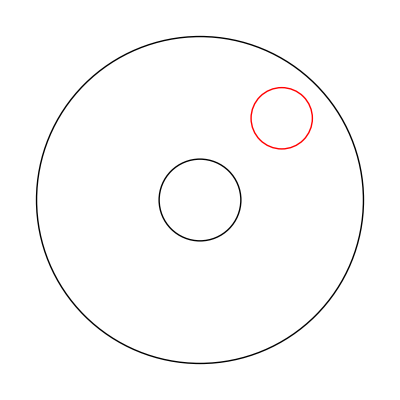

```mathematica
cir1=Graphics[Circle[{0,0},0.8]];
cir2=Graphics[Circle[{0,0},0.2]];
cir3=Graphics[{Red,Circle[{0.4,0.4},0.15]}];
Show[{cir1,cir2,cir3}]
```

```mathematica
q={θ1[t],θ2[t]}
dq=D[q,t]
subsrule = Inner[Rule, {θ1, θ2}, q, List]
```

{θ1[t],θ2[t]}

{θ1'[t],θ2'[t]}

{θ1→θ1[t],θ2→θ2[t]}

```mathematica
cml1={(l1/2)Cos[θ1[t]],(l1/2)Sin[θ1[t]]}
cml2={l1 Cos[θ1[t]]+(l2/2)Cos[q[[1]]+θ2[t]],l1 Sin[θ1[t]]+(l2/2)Sin[θ1[t]+θ2[t]]}
```

{1/2 l1 Cos[θ1[t]],1/2 l1 Sin[θ1[t]]}

{l1 Cos[θ1[t]]+1/2 l2 Cos[θ1[t]+θ2[t]],l1 Sin[θ1[t]]+1/2 l2 Sin[θ1[t]+θ2[t]]}

```mathematica
vc1=D[cml1,t]
vc2=D[cml2,t]
```

{-1/2 l1 Sin[θ1[t]] θ1'[t],1/2 l1 Cos[θ1[t]] θ1'[t]}

{-l1 Sin[θ1[t]] θ1'[t]-1/2 l2 Sin[θ1[t]+θ2[t]] (θ1'[t]+θ2'[t]),l1 Cos[θ1[t]] θ1'[t]+1/2 l2 Cos[θ1[t]+θ2[t]] (θ1'[t]+θ2'[t])}

```mathematica
ke1=Simplify[(1/2)m1(vc1.vc1)+(1/2)I1 dq[[1]]^2]
ke2=Simplify[Expand[(1/2)m2(vc2.vc2)+(1/2)I2 (dq[[1]]+dq[[2]])^2]]
```

1/8 (4 I1+l1^2 m1) θ1'[t]^2

1/8 ((4 I2+4 l1^2 m2+l2^2 m2+4 l1 l2 m2 Cos[θ2[t]]) θ1'[t]^2+2 (4 I2+l2^2 m2+2 l1 l2 m2 Cos[θ2[t]]) θ1'[t] θ2'[t]+(4 I2+l2^2 m2) θ2'[t]^2)

```mathematica
ke=Simplify [ke1+ke2]
```

1/8 ((4 I1+4 I2+l1^2 m1+4 l1^2 m2+l2^2 m2+4 l1 l2 m2 Cos[θ2[t]]) θ1'[t]^2+2 (4 I2+l2^2 m2+2 l1 l2 m2 Cos[θ2[t]]) θ1'[t] θ2'[t]+(4 I2+l2^2 m2) θ2'[t]^2)

```mathematica
v=m1 g (l1/2 )Sin[q[[1]]]+m2 g (l1 Sin[q[[1]]]+(l2/2)Sin[q[[1]]+q[[2]]])
```

1/2 g l1 m1 Sin[θ1[t]]+g m2 (l1 Sin[θ1[t]]+1/2 l2 Sin[θ1[t]+θ2[t]])

```mathematica
L=ke-v
```

-1/2 g l1 m1 Sin[θ1[t]]-g m2 (l1 Sin[θ1[t]]+1/2 l2 Sin[θ1[t]+θ2[t]])+1/8 ((4 I1+4 I2+l1^2 m1+4 l1^2 m2+l2^2 m2+4 l1 l2 m2 Cos[θ2[t]]) θ1'[t]^2+2 (4 I2+l2^2 m2+2 l1 l2 m2 Cos[θ2[t]]) θ1'[t] θ2'[t]+(4 I2+l2^2 m2) θ2'[t]^2)

```mathematica
eq1=Simplify[Expand[D[D[L,dq[[1]]],t]-D[L,q[[1]]]]]
eq2=Simplify[Expand[D[D[L,dq[[2]]],t]-D[L,q[[2]]]]]
```

1/4 (2 g l1 m1 Cos[θ1[t]]+4 g l1 m2 Cos[θ1[t]]+2 g l2 m2 Cos[θ1[t]+θ2[t]]-4 l1 l2 m2 Sin[θ2[t]] θ1'[t] θ2'[t]-2 l1 l2 m2 Sin[θ2[t]] θ2'[t]^2+4 I1 θ1''[t]+4 I2 θ1''[t]+l1^2 m1 θ1''[t]+4 l1^2 m2 θ1''[t]+l2^2 m2 θ1''[t]+4 l1 l2 m2 Cos[θ2[t]] θ1''[t]+4 I2 θ2''[t]+l2^2 m2 θ2''[t]+2 l1 l2 m2 Cos[θ2[t]] θ2''[t])

1/4 (2 g l2 m2 Cos[θ1[t]+θ2[t]]+2 l1 l2 m2 Sin[θ2[t]] θ1'[t]^2+(4 I2+l2^2 m2+2 l1 l2 m2 Cos[θ2[t]]) θ1''[t]+4 I2 θ2''[t]+l2^2 m2 θ2''[t])

```mathematica
M={{Coefficient[eq1,θ1''[t]],Coefficient[eq1,θ2''[t]]},{Coefficient[eq2,θ1''[t]],Coefficient[eq2,θ2''[t]]}}
```

{{1/4 (4 I1+4 I2+l1^2 m1+4 l1^2 m2+l2^2 m2+4 l1 l2 m2 Cos[θ2[t]]),1/4 (4 I2+l2^2 m2+2 l1 l2 m2 Cos[θ2[t]])},{1/4 (4 I2+l2^2 m2+2 l1 l2 m2 Cos[θ2[t]]),1/4 (4 I2+l2^2 m2)}}

```mathematica
MatrixForm[M]
```

(1/4 (4 I1+4 I2+l1^2 m1+4 l1^2 m2+l2^2 m2+4 l1 l2 m2 Cos[θ2[t]]) | 1/4 (4 I2+l2^2 m2+2 l1 l2 m2 Cos[θ2[t]])
1/4 (4 I2+l2^2 m2+2 l1 l2 m2 Cos[θ2[t]]) | 1/4 (4 I2+l2^2 m2))

```mathematica
Simplify[M-Transpose[M]]
```

{{0,0},{0,0}}

```mathematica
eq1subs=eq1/.param/.massparam
eq2subs=eq2/.param/.massparam
```

1/4 (0.205738 Cos[θ1[t]]+0.0336662 Cos[θ1[t]+θ2[t]]-0.00343533 Sin[θ2[t]] θ1'[t] θ2'[t]-0.00171767 Sin[θ2[t]] θ2'[t]^2+0.00970799 θ1''[t]+0.00343533 Cos[θ2[t]] θ1''[t]+0.000801577 θ2''[t]+0.00171767 Cos[θ2[t]] θ2''[t])

1/4 (0.0336662 Cos[θ1[t]+θ2[t]]+0.00171767 Sin[θ2[t]] θ1'[t]^2+(0.000801577+0.00171767 Cos[θ2[t]]) θ1''[t]+0.000801577 θ2''[t])

```mathematica
τ1=0.5*Sin[0.5*t];τ2=0.30*Sin[0.5*t];tf=1;
```

```mathematica
s=NDSolve[{{eq1subs,eq2subs}-{τ1,τ2}=={0,0},θ1[0]==π/4,θ2[0]==π/3,θ1'[0]==0,θ2'[0]==0},{θ1,θ2},{t,0,tf}]
```

{{θ1→InterpolatingFunction[…],θ2→InterpolatingFunction[…]}}

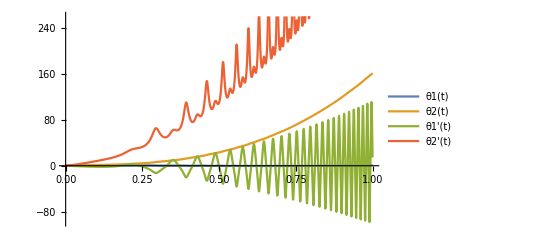

```mathematica
Plot[Evaluate[{θ1[t],θ2[t],θ1'[t],θ2'[t]}/. s],{t,0,tf},PlotStyle->Automatic,PlotLegends->{θ1[t],θ2[t],θ1'[t],θ2'[t]}]
```

## Trajectory planning

```mathematica
(*Determining cubic trajectory coefficients*)
initconds={ϕ0->0,ϕf->2π,dϕ0->0,dϕf->0};
traj=a0+a1 t+a2 t^2+a3 t^3;
dtraj=D[traj,t];
eq1traj=(traj/.{t->0})-ϕ0;
eq2traj=(traj/.{t->tF})-ϕf;
eq3traj=(dtraj/.{t->0})-dϕ0;
eq4traj=(dtraj/.{t->tF})-dϕf;
solcoeff=Solve[{eq1traj,eq2traj,eq3traj,eq4traj}==0,{a0,a1,a2,a3}][[1]]
trajf=traj/.solcoeff/.initconds
dtrajf=D[trajf,t]
```

{a0→ϕ0,a1→dϕ0,a2→-(2 dϕ0 tF+dϕf tF+3 ϕ0-3 ϕf)/tF^2,a3→-(-dϕ0 tF-dϕf tF-2 ϕ0+2 ϕf)/tF^3}

-(4 π t^3)/tF^3+(6 π t^2)/tF^2

-(12 π t^2)/tF^3+(12 π t)/tF^2

```mathematica
(*Determining position velocity and acceleration on the circular trajectory*)
n=0.1;
TF=10;
(*pathparams={xc->0.4,yc->0.4,a->0.30,b->0.10tF->TF};
xpos=(xc+a Cos[ϕ])/.{ϕ->trajf}/.pathparams;
ypos=(yc+b Sin[ϕ])/.{ϕ->trajf}/.pathparams;
pos={xpos,ypos}
pathvel=D[pos,t]
pathacc=D[pathvel,t]*)
pathparams={xc->0.4,yc->0.4,r->0.15,tF->TF};
xpos=(xc+r Cos[ϕ])/.{ϕ->trajf}/.pathparams;
ypos=(yc+r Sin[ϕ])/.{ϕ->trajf}/.pathparams;
pos={xpos,ypos}
pathvel=D[pos,t]
pathacc=D[pathvel,t]
```

{0.4+0.15 Cos[(3 π t^2)/50-(π t^3)/250],0.4+0.15 Sin[(3 π t^2)/50-(π t^3)/250]}

{-0.15 ((3 π t)/25-(3 π t^2)/250) Sin[(3 π t^2)/50-(π t^3)/250],0.15 ((3 π t)/25-(3 π t^2)/250) Cos[(3 π t^2)/50-(π t^3)/250]}

{-0.15 ((3 π t)/25-(3 π t^2)/250)^2 Cos[(3 π t^2)/50-(π t^3)/250]-0.15 ((3 π)/25-(3 π t)/125) Sin[(3 π t^2)/50-(π t^3)/250],0.15 ((3 π)/25-(3 π t)/125) Cos[(3 π t^2)/50-(π t^3)/250]-0.15 ((3 π t)/25-(3 π t^2)/250)^2 Sin[(3 π t^2)/50-(π t^3)/250]}

```mathematica
(*Discretizing position velocity and acceleration on the circular trajectory in task space*)

posv=Table[pos,{t,0,TF,n}];
velv=Table[pathvel,{t,0,TF,n}];
accv=Table[pathacc,{t,0,TF,n}];
```

## Inverse Dynamics

```mathematica
(*Performing inverse kinematics on the task space coordinates to find the corresponding joint space angles*)
```

```mathematica
jointpos=Table[(IK[{l1,l2,x,y,θ1,θ2}]/.param/.{x->posv[[ii]][[1]],y->posv[[ii]][[2]]})[[1]],{ii,1,(TF/n)+1}];
```

```mathematica
(*Computing jacobian of the end effector*)
```

```mathematica
endeffpos={l1 Cos[θ1]+l2 Cos[θ1+θ2],l1 Sin[θ1]+l2 Sin[θ1+θ2]};
J=D[endeffpos,{{θ1,θ2}}];
invJ=Inverse[J];
MatrixForm[J];
```

```mathematica
(*Computing the joint velocities for the particular task space trajectory*)
```

```mathematica
dθ = Table[Inverse[J/.param/.jointpos[[ii]]].velv[[ii]],{ii,1,(TF/n)+1}];
```

```mathematica
dJ = D[J/.subsrule, t];
```

```mathematica
Jdotθdot=dJ.{θ1'[t],θ2'[t]};
```

```mathematica
dθmap = Table[{θ1'[t]->dθ[[ii]][[1]], θ2'[t]->dθ[[ii]][[2]]},{ii,1,(TF/n)+1}];
```

```mathematica
(*Jdot=Table[dJ/.param/.(jointpos[[ii]]/.subsrule)/.dθmap[[ii]],{ii,1,11}]*)
```

```mathematica
Jdotθdotv=Table[Jdotθdot/.param/.(jointpos[[ii]]/.subsrule)/.dθmap[[ii]],{ii,1,(TF/n)+1}];
```

```mathematica
ddθ=Table[(invJ.(accv[[ii]]-Jdotθdotv[[ii]]))/.param/.jointpos[[ii]],{ii,1,(TF/n)+1}];
```

```mathematica
ddθmap = Table[{θ1''[t]->ddθ[[ii]][[1]], θ2''[t]->ddθ[[ii]][[2]]},{ii,1,(TF/n)+1}];
```

```mathematica
θmap=jointpos/.subsrule;
```

```mathematica
tau1=Table[(eq1subs/.θmap[[ii]]/.dθmap[[ii]]/.ddθmap[[ii]]),{ii,1,(TF/n)+1}];
```

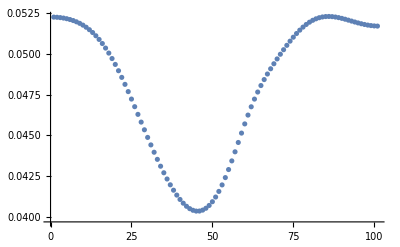

```mathematica
ListPlot[tau1]
```

```mathematica
tau2=Table[(eq2subs/.θmap[[ii]]/.dθmap[[ii]]/.ddθmap[[ii]]),{ii,1,(TF/n)+1}];
```

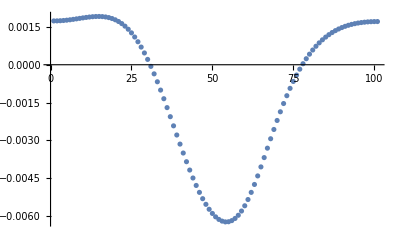

```mathematica
ListPlot[tau2]
```